# Minkowski Worldline with Equal Proper-Time Markers

c = 1 ly/year. Proper acceleration: +100 g for 0–10 years, −100 g for 10–20 years, then 0.

```mathematica
(*Define acceleration and solve for x(τ),t(τ) from proper time*)
Clear[x,t,eta,a,tau];
g=9.80665;                (*m/s^2*)
c=299792458;              (*m/s*)
yearSec=365.25*24*3600;   (*s/year*)
a0=.3;   (*ly/year^2 1 ly/year==c*)
ag=a0 * yearSec * c / yearSec^2 / g (*acceleration in g*)
```

0.290615

```mathematica
(*proper-acceleration profile*)
a[tau_]:=Piecewise[{{a0,0<=tau<5},{-a0,5<=tau<15},{a0,15<=tau<20}},0];
```

```mathematica
(*integrate rapidity->velocity->worldline*){xCoord,tCoord,etaFun}=NDSolveValue[{x'[tau]==Sinh[eta[tau]],t'[tau]==Cosh[eta[tau]],eta'[tau]==a[tau],x[0]==0,t[0]==0,eta[0]==0},{x,t,eta},{tau,0,25}];
```

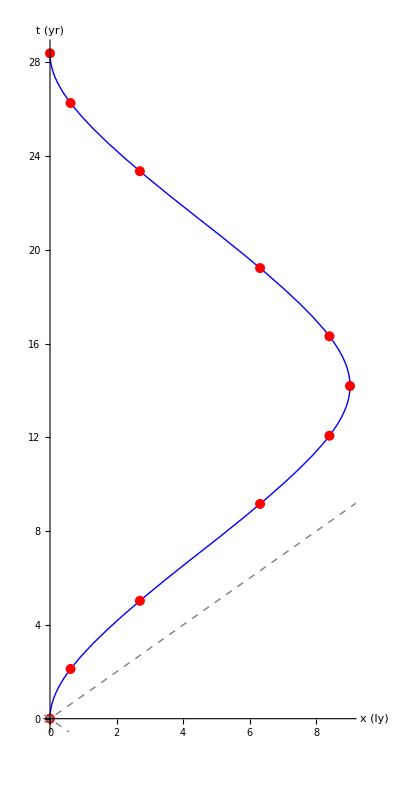

```mathematica
(*Plot worldline with equal-Δτ markers*)
Module[{Npts,tauMax,tauMarks,pts},Npts=10;
tauMax=20;(*covers both acceleration segments*)
tauMarks=Subdivide[0,tauMax,Npts];
pts={xCoord[#],tCoord[#]}&/@tauMarks;
ParametricPlot[{xCoord[tau],tCoord[tau]},{tau,0,tauMax},
PlotStyle->{Thick,Blue},
PlotRange->All,
AxesLabel->{"x (ly)","t (yr)"},
AspectRatio->2,
Epilog->{
Red,
PointSize[0.018],
Point[pts],
Gray,
PointSize[0.012],
Point[{0,0}],
Directive[Gray,Dashed],
Line[{{-30,-30},{30,30}}],
Line[{{-30,30},{30,-30}}]
}
]
]
```

Second plot: instantaneous simultaneity lines through each marker.

```mathematica
(*Simultaneity lines t = v x + b, v = tanh η*)
Module[{Npts,tauMax,tauMarks,pts,vAt,bAt,xrange,trange,worldline,simultLines},
Npts=10;
tauMax=20;
tauMarks=Subdivide[0,tauMax,Npts];
pts={xCoord[#],tCoord[#]}&/@tauMarks;
vAt[tau_]:=Tanh[etaFun[tau]];(* instantaneous velocity *)
bAt[tau_]:=tCoord[tau]-vAt[tau] xCoord[tau];(* intercept for t=v x+b at each τ *)
xrange={-5,15};
trange={0,25};
worldline=ParametricPlot[{xCoord[tau],tCoord[tau]},{tau,0,tauMax},PlotStyle->{Thick,Blue},PlotRange->{xrange,trange},AxesLabel->{"x (ly)","t (yr)"},AspectRatio->2];
simultLines=Graphics[Table[Module[{v,b,x1,x2},v=vAt[t];b=bAt[t];
x1=xrange[[1]];x2=xrange[[2]];
{Directive[Orange,Dashed,Thin],Line[{{x1,v x1+b},{x2,v x2+b}}],Black,PointSize[0.016],Point[{0,b}]}],{t,tauMarks}]];
Show[worldline,Graphics[{Red,PointSize[0.018],Point[pts],Gray,PointSize[0.012],Point[{0,0}],Directive[Gray,Dashed],Line[{{-30,-30},{30,30}}],Line[{{-30,30},{30,-30}}]}],simultLines,PlotRange->{xrange,trange}]
]
```